{/1/m,/1/n,/1/rhoReOut,/1/t}

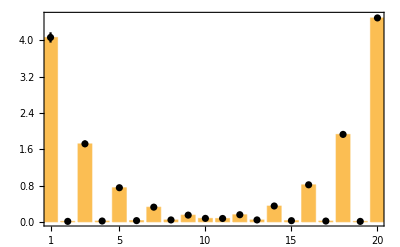

C:\Users\sturg\OneDrive\Documents\Ubuntu\published_version\Figure4\Figure4b\edge_states_sim_2.pdf

```mathematica
ClearAll["Global`*"];
Needs["ErrorBarPlots`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,FontColor->Black};
SetOptions[ListPlot,BaseStyle->texStyle,Frame->True,Axes->False,Joined->True,PlotRange->All];
SetDirectory[NotebookDirectory[]];
latestRun=Select[FileNames["run*","",Infinity],DirectoryQ][[-1]];
SetDirectory[latestRun];
noReps=ToExpression@Import["noreps.txt","Data"][[1]];
Import["0.h5"]
import[n_]:=Module[{data},
data=Import[ToString[n]<>".h5",{"Data",3}];
data=data[[-1]];
data=Diagonal[data]
]
data=import/@Range[noReps];
data=data//Transpose;
mean=Mean/@data;
stdev=StandardDeviation/@data ;
info={mean,stdev}//Transpose;
errors=ErrorListPlot[info,Joined->False,PlotStyle->Directive[Black]];
ticks=Table[{x,If[MemberQ[{1,5,10,15,20},x],x,""]},{x,1,20}];
chart=Show[BarChart[mean,PlotRange->All,FrameLabel->MaTeX/@{"\\text{Cavity number ($m$)}","\\text{$\\rho_m$ (a.u.)}"}],FrameTicks->{{Automatic,Automatic},{ticks,Automatic}},PlotRange->{{1,20},Automatic}];
figure=Show[chart,errors,PlotRangePadding->{{1,1},{0,1.8}}]
Export[NotebookDirectory[]<>"edge_states_sim_2.pdf",figure]
```

```mathematica
{"2"}
Range[2]
```

{2}

{1,2}

```mathematica
noReps=Import["noreps.txt","Data"][[1]]
noReps+1
```

2

1+2